```mathematica
CircleTimes=KroneckerProduct;
$Assumptions=Element[{θ,ϕ}, Reals]
```

(θ|ϕ)∈ℝ

```mathematica
a={{0,1},{0,0}};
ad={{0,0},{1,0}};
I2 = IdentityMatrix[2];
```

```mathematica
UBS={{Exp[ⅈ ϕ]Cos[θ], -Sin[θ]},{Exp[ⅈ ϕ]Sin[θ],Cos[θ]}};
LogUBS =-ⅈ MatrixLog[UBS];
```

```mathematica
H=LogUBS[[1,1]] (ad.a)⊗I2 + LogUBS[[1,2]](ad⊗a) + LogUBS[[2,1]](a⊗ad)+LogUBS[[2,2]](I2⊗(ad.a));
```

```mathematica
M=MatrixExp[ⅈ H];
```

```mathematica
M/.{θ->0.1,ϕ->0.1} //MatrixForm
```

(1 | 0 | 0 | 0
0 | 0.995004-4.30211×10^-16 ⅈ | 0.0993347+0.00996671 ⅈ | 0
0 | -0.0998334+1.11022×10^-16 ⅈ | 0.990033+0.0993347 ⅈ | 0
0 | 0 | 0 | 0.995004+0.0998334 ⅈ)

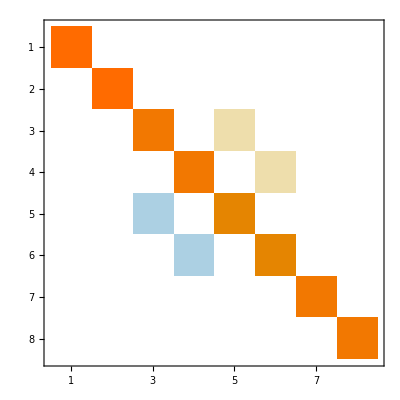

```mathematica
MatrixPlot[M⊗I2 /.{θ->0.1, ϕ->0.1}]
```

```mathematica
(*What if now we add an ancilla mode?*)
```

```mathematica
UBS…anc={{Exp[ⅈ ϕ]Cos[θ], -Sin[θ],0},{Exp[ⅈ ϕ]Sin[θ],Cos[θ],0},{0,0,1}};
```

```mathematica
%//MatrixForm
```

(ⅇ^(ⅈ ϕ) Cos[θ] | -Sin[θ] | 0
ⅇ^(ⅈ ϕ) Sin[θ] | Cos[θ] | 0
0 | 0 | 1)

```mathematica
LogUBS…anc=-ⅈ MatrixLog[UBS…anc];
```

```mathematica
H…anc=LogUBS…anc[[1,1]] (ad.a)⊗I2⊗I2 + LogUBS…anc[[1,2]] ad⊗a⊗I2 +LogUBS…anc[[2,1]] a⊗ad⊗I2+LogUBS…anc[[2,2]] I2⊗(ad.a)⊗I2;
```

```mathematica
M…anc=MatrixExp[ⅈ H…anc];
```

```mathematica
MatrixPlot[M…anc /.{θ->0.1,ϕ->0.1}]
```

-Graphics-

```mathematica
M⊗I2/.{θ->0.1, ϕ->0.1}//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.995004-4.30211×10^-16 ⅈ | 0 | 0.0993347+0.00996671 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0.995004-4.30211×10^-16 ⅈ | 0 | 0.0993347+0.00996671 ⅈ | 0 | 0
0 | 0 | -0.0998334+1.11022×10^-16 ⅈ | 0 | 0.990033+0.0993347 ⅈ | 0 | 0 | 0
0 | 0 | 0 | -0.0998334+1.11022×10^-16 ⅈ | 0 | 0.990033+0.0993347 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.995004+0.0998334 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.995004+0.0998334 ⅈ)

```mathematica
M…anc /.{θ->0.1,ϕ->0.1} //MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.995004-4.30211×10^-16 ⅈ | 0 | 0.0993347+0.00996671 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0.995004-4.30211×10^-16 ⅈ | 0 | 0.0993347+0.00996671 ⅈ | 0 | 0
0 | 0 | -0.0998334+1.11022×10^-16 ⅈ | 0 | 0.990033+0.0993347 ⅈ | 0 | 0 | 0
0 | 0 | 0 | -0.0998334+1.11022×10^-16 ⅈ | 0 | 0.990033+0.0993347 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.995004+0.0998334 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.995004+0.0998334 ⅈ)

```mathematica
(*Extra tests*)
```